### Start choosing the example:

```mathematica
t="Jamaratv9";
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
```

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
{timedata,d2e}=AbsoluteTiming@D2E[Data/.{I1-> 20,I2->200000, U1-> 200,U2->100,U3->0}];
timedata
{time,{system,rules}}=AbsoluteTiming@CriticalCongestionSolver[d2e];
time
```

0.119162

Number of variables: 118

Removed variables: 98

Time to "eliminate" u variables: 1.56647 seconds and

Removed variables: 103

Removed variables: 103

2.13527

```mathematica
system
```

True

```mathematica
AllTrue
```

```mathematica
{time,rules}=AbsoluteTiming@Solver[d2e][alpha=1];
time
```

The error (1-Norm of LHS-RHS) is 3.63043×10^-14

The error is 3.63043×10^-14 which is less than 1.×10^-10

It took 6.46393 seconds to solve!
	The system is True

6.46547

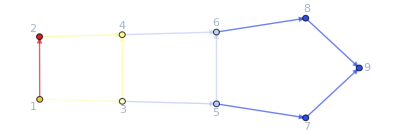

```mathematica
ColorNetworkByValueFunctionOperator[d2e][rules]
```

```mathematica
{timedata,d2e}=AbsoluteTiming[D2E[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}]];
timedata;
{time,{system,result}}=AbsoluteTiming@CriticalCongestionSolver[d2e];
time
```

Number of variables: 118

Removed variables: 98

Time to "eliminate" u variables: 1.64716 seconds and

Removed variables: 102

Removed variables: 102

2.3308

```mathematica
result=Solver[d2e][alpha=1];
```

The error (1-Norm of LHS-RHS) is 1.20737×10^-14

The error is 1.20737×10^-14 which is less than 1.×10^-10

It took 5.54414 seconds to solve!
	The system is True

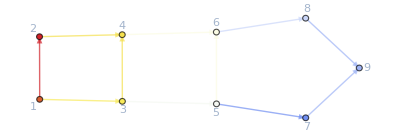

```mathematica
ColorNetworkByValueFunctionOperator[d2e][result]
```

```mathematica
d2e=D2E[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

Number of variables: 118

Removed variables: 98

Time to "eliminate" u variables: 1.49544 seconds and

Removed variables: 103

Removed variables: 103

2.03588

```mathematica
{time,d2e}=AbsoluteTiming@D2E[Data/.{I1-> 2.00000000001515151515151515115151515115151515151551515151,I2->6, U1-> 3,U2->3,U3->0.}];
time
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

0.116505

Number of variables: 118

Removed variables: 98

Time to "eliminate" u variables: 1.45041 seconds and

Removed variables: 103

Removed variables: 103

1.99183

#### Non-linear case

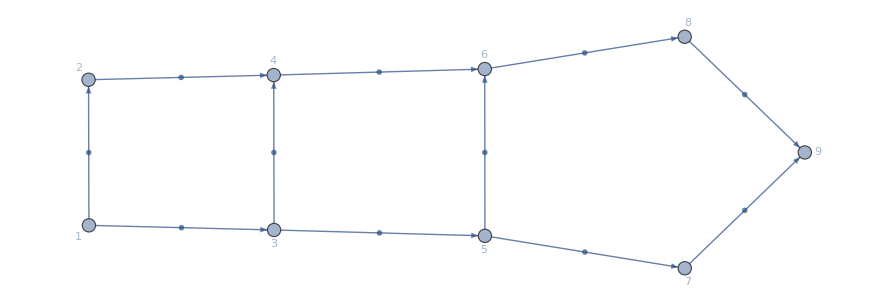

-Graphics-

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
MFGEquations = d2e;
FFR=rules;
BEL=EdgeList[MFGEquations["BG"]];
pop=(#-> Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,2.4},*)GridLines->Automatic,ImageSize->90])&/@BEL;
val=(#-> Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,4.7},*)GridLines->Automatic,ImageSize->90])&/@BEL;
Graph[MFGEquations["BG"],EdgeLabels-> pop,GraphLayout->"SpringElectricalEmbedding"]
Graph[MFGEquations["BG"],EdgeLabels-> val,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Solver[d2e][alpha = .1]
(*{timeFFR,FFR}= AbsoluteTiming[Catch@FixedPoint[FixedReduceX1[d2e1],rules1,200]//N//KeySort]*)
```

### The nonlinear solver solves the critical congestion case when the alpha is 1 and the initial currents are all zero.

```mathematica
rules0=AssociationThread[Values@d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]]
```

```mathematica
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
```

```mathematica
rules0=AssociationThread[Values @ d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@KeySort@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
d2e["EqCriticalCase"]/.FFR
```

### Test on a “large” network

#### D2E already takes half a minute. Set the option of giving the Graph with GridGraph, for example. Would this run faster?

```mathematica
eme=4;
ege=3;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
systemgrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

Number of variables: 152

Removed variables: 119

Time to "eliminate" u variables: 0.035018 seconds and

Removed variables: 121

Removed variables: 121

$Aborted

9.24611

0≤jt22≤1

-Graphics-

Number of variables: 82

Removed variables: 68

Time to "eliminate" u variables: 0.772157 seconds and

Removed variables: 71

Removed variables: 71

Removed variables: 81

It took 1.07221 seconds to solve the critical congestion case.

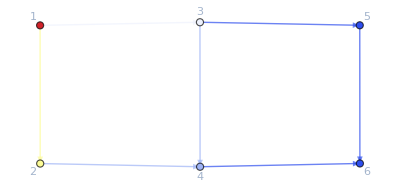

```mathematica
eme=2;
ege=3;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege,U1}/.U1->0, {eme*ege-1,0}, {eme*ege-2,U2}/.U2->100},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
Print["It took ",timegrid, " seconds to solve the critical congestion case."];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
rulesgridsolver = Solver[d2egrid][alpha=1];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgridsolver]
```

The error (1-Norm of LHS-RHS) is 9.9476×10^-13

The error is 9.9476×10^-13 which is less than 1.×10^-10

It took 3.40957 seconds to solve!
	The system is 200/7≤jt16≤100

-Graphics-

```mathematica
gr=GridGraph[{3,7},DirectedEdges->True, VertexLabels->"Name"];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{8,I1}/.I1->400},(*FinalCosts=*){{17,U1}/.U1->0},(*SwitchingCostsData=*){}}];
```

```mathematica
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data]
```

```mathematica
d2egrid["EqAllAll"]
```

```mathematica
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
gr=GridGraph[{3,3},DirectedEdges->True];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4,{3,4}},(*FinalCosts=*){{5,U1}/.U1->0(*,{8,0}*)},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data];
alpha=1;
(rulesgrid = Solver[d2egrid][alpha]);
```

```mathematica
{timegrid,{systemgrid,rulesgrid}}=AbsoluteTiming@CriticalCongestionSolver[d2egrid];
timegrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
rulesgrid=KeySort@rulesgrid;
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
rules0=AssociationThread[d2egrid["js"],Table[0,{i,1,Length@d2egrid["js"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2egrid],rules0, 1]
d2egrid["EqCriticalCase"]/.FFR
```

# TestZone

```mathematica
EqAllAll=Lookup[d2egrid,"EqAllAll",Print["No equations to solve."];
Return[]];
EqCriticalCase=Lookup[d2egrid,"EqCriticalCase",Print["Critical case equations are missing."];
Return[]];
InitRules=Lookup[d2egrid,"BoundaryRules",Print["Need boundary conditions"];];
```

```mathematica
{system,rules}=CleanEqualities[{EqCriticalCase&&EqAllAll,InitRules}];
```

```mathematica
Length[d2egrid["AllEq"]]
Length[d2egrid["AllEq"]/.rules]
Length[d2egrid["AllOr"]]
Length[d2egrid["AllOr"]/.rules]
Length[d2egrid["AllIneq"]]
Length[d2egrid["AllIneq"]/.rules]
Length[d2egrid["EqCriticalCase"]]
Length[d2egrid["EqCriticalCase"]/.rules]
```

#### This is the winning code!

```mathematica
{system,rules}=((And@@(NewReduce/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["uvars"]]))//Simplify)&&system)//CleanEqualities
```

{(100+j17==j19||j19==j8)&&(100+j17==j8||j19==j8)&&(100+7 j13+j17+j19==1200+7 j14+j17+j8||2900+5 j17+2 j19==2400+5 (100+j17)+2 j8)&&(2900+5 j17+2 j19==2400+5 (100+j17)+2 j8||100+2 j13+j17==2900/7+2 j14+j17)&&1200/7+j14+1/7 (-100-j17)+j17/7-j19/7+j8/7≥0&&1600/7+j13-j17/7+(100+j17)/7+j19/7-j8/7≥0&&1200/7+j14+1/7 (-100-j17)+j17/7-j19/7+j8/7≥0&&800/7+j15+(3 j17)/7-(3 (100+j17))/7-(3 j19)/7+(3 j8)/7≥0&&800/7-(4 j17)/7+(4 (100+j17))/7+(4 j19)/7-(4 j8)/7+jt29≥0&&100+j17≥0&&2000/7+(11 j17)/7-(11 (100+j17))/7-(4 j19)/7+(4 j8)/7≥0&&j8≥0&&800/7-(4 j17)/7+(4 (100+j17))/7+(11 j19)/7-(11 j8)/7≥0&&100-j19+j8≥0&&j14≥0&&j13≥0&&j14≥0&&j15≥0&&jt29≥0&&j17≥0&&j19≥0&&j14≥0&&j13≥0&&1200/7-j13+j14+1/7 (-100-j17)+j17/7-j19/7+j8/7≥0&&1600/7+j13-j14-j17/7+(100+j17)/7+j19/7-j8/7≥0&&1200/7+j14+1/7 (-100-j17)+j17/7-j19/7+j8/7≥0&&j14≥0&&800/7+j15+(3 j17)/7-(3 (100+j17))/7-(3 j19)/7+(3 j8)/7+jt13-jt29≥0&&800/7+j13-j15-(4 j17)/7+(4 (100+j17))/7+(4 j19)/7-(4 j8)/7-jt13+jt29≥0&&j13-jt13≥0&&-j13+j15+jt13≥0&&jt13≥0&&-jt13+jt29≥0&&j15-jt22≥0&&jt16≥0&&1200/7+j14-j15+1/7 (-100-j17)+j17/7-j19/7+j8/7-jt16+jt22≥0&&j14-jt21≥0&&100+j17-jt16≥0&&800/7-j14+j15+(3 j17)/7-(10 (100+j17))/7-(3 j19)/7+(3 j8)/7+jt16+jt21≥0&&jt21≥0&&jt22≥0&&j17-jt21-jt22≥0&&j8≥0&&800/7-(4 j17)/7+(4 (100+j17))/7+(4 j19)/7-(11 j8)/7+jt29≥0&&jt29≥0&&j19-jt29≥0&&j19≥0&&100+j17-j19≥0&&j17≥0&&-j17+j8≥0&&2400/7-(5 j17)/7+(5 (100+j17))/7-(2 j19)/7+(2 j8)/7≥2900/7&&-j19+j8≤0&&(j14==0||1200/7+j14+1/7 (-100-j17)+j17/7-j19/7+j8/7==0)&&(j13==0||1600/7+j13-j17/7+(100+j17)/7+j19/7-j8/7==0)&&(j14==0||1200/7+j14+1/7 (-100-j17)+j17/7-j19/7+j8/7==0)&&(j15==0||800/7+j15+(3 j17)/7-(3 (100+j17))/7-(3 j19)/7+(3 j8)/7==0)&&(jt29==0||800/7-(4 j17)/7+(4 (100+j17))/7+(4 j19)/7-(4 j8)/7+jt29==0)&&(j17==0||100+j17==0)&&(j19==0||j8==0)&&(j14==0||j13==0)&&(800/7+j13-j15-(4 j17)/7+(4 (100+j17))/7+(4 j19)/7-(4 j8)/7-jt13+jt29==0||jt13==0)&&(j13-jt13==0||800/7+j15+(3 j17)/7-(3 (100+j17))/7-(3 j19)/7+(3 j8)/7+jt13-jt29==0)&&(-j13+j15+jt13==0||-jt13+jt29==0)&&(j15-jt22==0||j14-jt21==0)&&(jt16==0||jt21==0)&&(100+j17-jt16==0||jt22==0)&&(j8==0||jt29==0)&&(j19==0||j17==0)&&(1200/7+j14+1/7 (-100-j17)+j17/7-j19/7+j8/7==0||j14==0)&&(1200/7-j13+j14+1/7 (-100-j17)+j17/7-j19/7+j8/7==0||-500/7-(5 j17)/7+(5 (100+j17))/7-(2 j19)/7+(2 j8)/7==0)&&(1600/7+j13-j14-j17/7+(100+j17)/7+j19/7-j8/7==0||-500/7-(5 j17)/7+(5 (100+j17))/7-(2 j19)/7+(2 j8)/7==0)&&(800/7-(4 j17)/7+(4 (100+j17))/7+(4 j19)/7-(11 j8)/7+jt29==0||j19-j8==0)&&(j19-jt29==0||j19-j8==0),<|j6→100+j17,u11→2900/7,u19→0|>}

# This is in the code already:

### Color representation of the value function (this is suitable for the critical congestion case because the value function is linear on each edge)

#### New function!!!

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}

ColorNetworkByValueFunctionOperator[d2e1_Association][rules_]:= Module[{values,colors},
values=d2e1["VL"]/.KeyMap[#[[1]]&,d2e1["uvars"]/.rules];(*this works WITHOUT switching costs*)
(*Print[values];*)
colors=ColorData["TemperatureMap"]/@(values/Max[values]);
(*Print[colors];*)
GraphicsGrid[{
{HighlightGraph[SetProperty[d2e1["BG"],EdgeShapeFunction-> eStyle[colors]],Thread[Style[d2e1["VL"],colors]],GraphLayout->"SpringElectricalEmbedding"]},
{BarLegend["TemperatureMap",LegendMarkerSize->100,LegendLayout->"ReversedRow"]}
}]
]
```

### Idea:

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}
g=GridGraph[{4,4},VertexLabels->"Name",ImagePadding->10,DirectedEdges->True];
colors=ColorData["TemperatureMap"]/@(VertexDegree[g]/Max[VertexDegree[g]]);
HighlightGraph[SetProperty[g,EdgeShapeFunction->eStyle[colors]],Thread[Style[VertexList[g],colors]]]
```

```mathematica
NewReduce@(And @@(Select[system,Function[a,FreeQ[a,#]]]&/@Values[d2egrid["jtvars"]]//DeleteDuplicates)//DeleteDuplicates)
```

```mathematica
BooleanConvert[%,"CNF"]
```

91 j1==16400&&7 j10==800&&91 j11==4300&&91 j12==9600&&91 j13==2000&&91 j14==14400&&91 j15==12400&&j16==100&&j18==0&&91 j2==20000&&j24==0&&j25==0&&j27==0&&j28==0&&j29==0&&j30==0&&jt10==0&&91 jt15==6100&&jt21==0&&(jt22==0||91 jt22==3700||jt22+jt25==3700/91)&&(jt22==0||91 jt22==3700||0≤jt22≤3700/91)&&(jt22==0||jt25==0||jt22+jt25==3700/91)&&(jt22==0||jt25==0||0≤jt22≤3700/91)&&(jt22==0||jt27==0)&&(91 jt22==3700||91 jt25==3700||jt22+jt25==3700/91)&&(91 jt22==3700||91 jt25==3700||0≤jt22≤3700/91)&&jt24==0&&(jt25==0||91 jt25==3700||jt22+jt25==3700/91)&&(jt25==0||91 jt25==3700||0≤jt22≤3700/91)&&(91 jt25==3700||jt27==0)&&(jt27==0||jt24+jt27==0)&&jt33==0&&91 jt39==4300&&jt45==0&&(jt46==0||91 jt46==2000||jt46+jt49==2000/91)&&(jt46==0||91 jt46==2000||0≤jt46≤2000/91)&&(jt46==0||jt49==0||jt46+jt49==2000/91)&&(jt46==0||jt49==0||0≤jt46≤2000/91)&&(jt46==0||jt51==0)&&(91 jt46==2000||91 jt49==2000||jt46+jt49==2000/91)&&(91 jt46==2000||91 jt49==2000||0≤jt46≤2000/91)&&jt48==0&&(jt49==0||91 jt49==2000||jt46+jt49==2000/91)&&(jt49==0||91 jt49==2000||0≤jt46≤2000/91)&&(91 jt49==2000||jt51==0)&&(jt51==0||jt48+jt51==0)&&jt57==0&&jt69==0&&jt70==0&&jt72==0

```mathematica
AbsoluteTiming[(NewReduce/@(Select[system,Function[a,!FreeQ[a,#]]]&/@ Values[d2egrid["jvars"]]))]
```

{3.72002,{(j2≤400&&j2≥0&&91 j25≤6700&&j25≥0&&91 j1==16400&&jt10==0&&j24==0)||(j2≤400&&j2≥0&&6700+91 j24≥0&&91 j1==16400&&j24==jt10&&j25==0)||(j2≤400&&j2≥0&&91 j1==16400&&91 jt10==9700&&91 j24==9700&&j25==0),(91 j2==20000&&j27==0&&91 j28==6100&&jt15==0&&j1≥0&&j1≤400)||(0≤j1≤400&&13900+91 j28≥0&&91 j2==20000&&j28+jt15==6100/91&&j27==0)||(0≤j1≤400&&91 j27≤13900&&j27≥0&&91 j2==20000&&6100/91+j27==jt15&&j28==0),True,True,True,True,True,True,True,38,True,True,True,True,True,True,True,True,True}}
 |  |  |  |

```mathematica
CleanEqualities[BooleanConvert[system,"CNF"]]
```

```mathematica
nn=3;
AbsoluteTiming[Select[system,Function[a,!FreeQ[a,#]]]&@ d2egrid["jvars"][[nn]]]
CleanEqualities[system&&(Select[system,Function[a,!FreeQ[a,#]]]&@ d2egrid["jvars"][[nn]])//NewReduce//BooleanConvert[#,"CNF"]&]
```

3

{0.000361,True}

{(jt22==0||91 jt22==3700||jt22+jt25==3700/91)&&(jt22==0||91 jt22==3700||0≤jt22≤3700/91)&&(jt22==0||jt25==0||jt22+jt25==3700/91)&&(jt22==0||jt25==0||0≤jt22≤3700/91)&&(jt22==0||jt27==0)&&(91 jt22==3700||91 jt25==3700||jt22+jt25==3700/91)&&(91 jt22==3700||91 jt25==3700||0≤jt22≤3700/91)&&(jt25==0||91 jt25==3700||jt22+jt25==3700/91)&&(jt25==0||91 jt25==3700||0≤jt22≤3700/91)&&(91 jt25==3700||jt27==0)&&(jt27==0||jt27==0)&&(jt46==0||91 jt46==2000||jt46+jt49==2000/91)&&(jt46==0||91 jt46==2000||0≤jt46≤2000/91)&&(jt46==0||jt49==0||jt46+jt49==2000/91)&&(jt46==0||jt49==0||0≤jt46≤2000/91)&&(jt46==0||jt51==0)&&(91 jt46==2000||91 jt49==2000||jt46+jt49==2000/91)&&(91 jt46==2000||91 jt49==2000||0≤jt46≤2000/91)&&(jt49==0||91 jt49==2000||jt46+jt49==2000/91)&&(jt49==0||91 jt49==2000||0≤jt46≤2000/91)&&(91 jt49==2000||jt51==0)&&(jt51==0||jt51==0),<|j1→16400/91,j10→800/7,j11→4300/91,j12→9600/91,j13→2000/91,j14→14400/91,j15→12400/91,j16→100,j18→0,j2→20000/91,j24→0,j25→0,j27→0,j28→0,j29→0,j30→0,jt10→0,jt15→6100/91,jt21→0,jt24→0,jt33→0,jt39→4300/91,jt45→0,jt48→0,jt57→0,jt69→0,jt70→0,jt72→0|>}

```mathematica
(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["jvars"]])
```

```mathematica
(And@@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["jvars"]])//BooleanConvert[#,"CNF"]&)
```

```mathematica
CriticalCongestionStep[%]
```